```mathematica
(* TEST: A + A <-> B *)
```

```mathematica
AVOGADRO=6.0221367*10^23;
Mtoperm3[molar_]= molar*(1000*AVOGADRO);
microMtoperm3[micromolar_]= Mtoperm3[micromolar/(1*10^6)];calckD[Diffusion_,sigma_]= 4.0*Pi*Diffusion*sigma;
calcka[konvar_,kDvar_]=1/((1/konvar)-(1/kDvar));
calckd[koffvar_,konvar_,kDvar_] =calcka[konvar,kDvar]*koffvar/konvar;
```

```mathematica
NA=300.;
NB=NA/3;
L=1*10^(-6);
VOLUME=L^3;
CONCENTRATIONA=NA / VOLUME;
CONCENTRATIONB= NB / VOLUME;
```

```mathematica
DA=1.0*10^-12;
RADIUSA=5.0*10^-9;

OFFSET =CONCENTRATIONB;
STARTA = CONCENTRATIONA +OFFSET;
STARTB = CONCENTRATIONB - OFFSET/2;
kon=1.*10^(-19)
koff=3/2.* kon*CONCENTRATIONA
kD=calckD[2*DA,2*RADIUSA];

kd=calckd[koff,kon,kD]
ka=calcka[kon,kD]

kon/koff;
ka/kd;
```

1.×10^-19

45.

74.7368

1.66082×10^-19

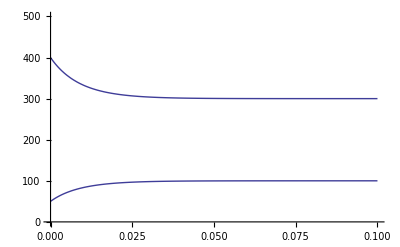

{300.003}

{99.9987}

```mathematica
ENDTIME = 0.1;
s = NDSolve[{A'[t]==-kon*(A[t]^2)+koff*2*B[t],B'[t]==-koff*B[t]+kon/2.*(A[t]^2), A[0]==STARTA, B[0]==STARTB}, {A, B}, {t, 0, ENDTIME}];
Plot[{A[t]*VOLUME, B[t]*VOLUME} /. s, {t, 0, ENDTIME},PlotRange->{0, 500}] 
A[ENDTIME]*VOLUME/.s
B[ENDTIME]*VOLUME/.s
```